## Quasinormal modes

We want to have a look at the quasinormal modes of an AdS black hole in 3+1 dimensions. The metric of this black hole is given by

	ds^2 = -f(r) dt^2 + (f(r))^-1 dr^2 + r^2  (dθ^2 + sin^2 θ dϕ^2)
with 
	f(r) = r^2/R^2+ 1 - r_0/r
	
where R is the AdS radius, set to 1 in this notebook, and r_0 is a constant related to the mass of the black hole.
In this background geometry, we want to look at the solutions of the scalar wave equation 

	∇_a ∇^a Φ = 0

### Thermalisation

Boundary conditions:

Φ(r -> +∞, v) -> 0

### Quasinormal modes

We can rewrite the metric in ingoing Eddington coordinates (v = t + r_*) as 

	ds^2 = -f(r) dv^2 + 2 dv dr + r^2  (dθ^2 + sin^2 θ dϕ^2)

```mathematica
coord = {v, r, θ, ϕ};
metric = {{-f[r], 1, 0, 0}, {1, 0, 0 , 0}, {0, 0, r^2, 0}, {0, 0, 0, r^2 Sin[θ]^2}};
$Assumptions = And[v∈Reals, r∈Reals, θ∈Reals, ϕ∈Reals];
SetDirectory["/home/silke/Documents/Wolfram Mathematica"]
<< diffgeo.m
```

/home/silke/Documents/Wolfram Mathematica

```mathematica
metric // MatrixForm
```

(-f[r] | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

Suppose we have solutions of the equation ∇_a ∇^a Φ = 0 given by

```mathematica
Φ[v, r] = 1/r ψ[r] Exp[-ⅈ ω v];
```

which leads to a radial equation for ψ.

```mathematica
gradient = partial[Φ[v, r]].inverse;
pde = divergence[gradient] == 0 //Simplify
```

(-2 ⅈ ω+f'[r]) ψ'[r]+f[r] ψ''[r]==(ψ[r] f'[r])/r

So we get as equation

	f(r) d^2/dr^2 ψ(r)  +  (-2 ⅈ ω + f'(r))  d/dr ψ(r) - (f'(r))/r ψ(r) = 0
	
consistent with equation (2.13) with V(r) = (f'(r))/r.

In order for the coordinate interval to be finite, we change to the coordinate x = 1/r, and using
	d/dr = dx/dr d/dx = -1/r^2 d/dx =  -x^2 d/dx
	
we get

	f(r) d^2/dr^2 ψ(r)  +  (-2 ⅈ ω + f'(r))  d/dr ψ(r) - (f'(r))/r ψ(r) = 0

f(r) x^2 d/dx(x^2 d/dx ψ(x))  -  (-2 ⅈ ω + f'(r))  x^2 d/dx ψ(r) - (f'(r))/r ψ(r) = 0

 f(r) x^4 d^2/dx^2 ψ(x) + (2 ⅈ ω x^2 - f'(r)x^2 + 2f(r)  x^3 )d/dx ψ(x) -  x f'(r)ψ(x) = 0
	
Now rewriting the function f(r):

	f(r) = r^2+ 1 - r_0/r  = 1/x^2+ 1 - r_0 x
f'(r) = 2r + r_0/r^2 = 2/x + r_0 x^2

2f(r) x^3 = 2x+ 2 x^3 - 2 r_0 x^4
f(r) x^4 = x^2+ x^4 - r_0 x^5
f'(x) x = 2 + r_0 x^3
-f'(x) x^2 = -2x - r_0 x^4 
	
So this gives

	f(r) x^4 d^2/dx^2 ψ(x) + (2 ⅈ ω x^2 - f'(r)x^2 + 2f(r)  x^3 )d/dx ψ(x) -  x f'(r)ψ(x) = 0

(x^2+ x^4 - r_0 x^5)d^2/dx^2 ψ(x) + (2 ⅈ ω x^2 - 2x - r_0 x^4 + 2x+ 2 x^3 - 2 r_0 x^4)d/dx ψ(x) -  (2 + r_0 x^3)ψ(x) = 0

(- r_0 x^5+ x^4+ x^2 )d^2/dx^2 ψ(x) + ( -3 r_0 x^4 + 2 x^3 + 2 ⅈ ω x^2)d/dx ψ(x) +  (- r_0 x^3 - 2)ψ(x) = 0

(+ r_0 x^5- x^4- x^2)/(x - xh)d^2/dx^2 ψ(x) + (3 r_0 x^4 - 2 x^3 - 2 ⅈ ω x^2)/(x - xh)d/dx ψ(x) +  ( r_0 x^3 + 2)/(x - xh)ψ(x) = 0         if x ≠ xh, where x_+ is the horizon radius satisfying r_0 = (xh^2 + 1)/xh^3

So we get as equation (3.1)

	s(x)d^2/dx^2 ψ(x) + (t(x))/(x - xh)d/dx ψ(x) +  (u(x))/(x - xh)^2 ψ(x) = 0         if x ≠ xh

	with
		s(x) =(r_0 x^5- x^4- x^2)/(x - xh)       (3.2)
		t(x) = 3 r_0 x^4 - 2 x^3 - 2 ⅈ ω x^2       (3.3)
		u(x) = (r_0 x^3 + 2)(x - xh) = f'(x) x (x - xh) = V(x) (x - xh)       (3.4)

```mathematica
rh=100;
xh=1/rh;
r0=1/xh^3+ 1/xh;
```

```mathematica
s[x_]:=(r0 x^5-x^4-x^2)/(x-xh);
t[x_, ω_]:=3 r0 x^4-2 x^3-2 x^2 ⅈ ω;
V[x_]:= 2 + r0 x^3;
u[x_]:=(x-xh)V[x];
```

We can expand these functions around the horizon, since they are polynomials of degree 4:

	s(x) = ∑_(n=0)^d s_n (x - xh)^n
t(x) = ∑_(n=0)^d t_n (x - xh)^n
u(x) = ∑_(n=0)^d u_n (x - xh)^n

```mathematica
coefs[n_]:=SeriesCoefficient[Series[s[x],{x,xh,n}],n];coefu[n_]:=SeriesCoefficient[Series[u[x],{x,xh,n}],n];coeft[n_]:=SeriesCoefficient[Series[t[x,ω],{x,xh,n}],n];
```

We also expand ψ(x) around the horizon:

	ψ(x) = ∑_(n=0)^∞ a_n (x - xh)^n

Substituting this in the equation we had before, we get:

	s(x) d^2/dx^2 ψ(x) + (t(x))/(x - xh) d/dx ψ(x) + (u(x))/(x - xh)^2 ψ(x) = 0
∑_m ∑_k [s_m (x - xh)^m a_k k(k-1) (x - xh)^(k-2) + t_m (x - xh)^m a_k k (x - xh)^(k-2) + u_m (x - xh)^m a_k (x - xh)^(k-2)] = 0
∑_m ∑_k [s_m a_k k(k-1) (x - xh)^(m+k-2) + t_m a_k k (x - xh)^(m+k-2) + u_m a_k (x - xh)^(m+k-2)] = 0

Substitute n = m +k, so we get 

	∑_n ∑_k [s_(n-k)a_k k(k-1) + t_(n-k) a_k k + u_(n-k) a_k] (x - xh)^(n-2)= 0
	
Since all terms in n are linear independent, and s_(n-k) = t_(n-k)=u_(n-k) = 0 for k > n, we get
	
	∑_(k=0)^n [s_(n-k)a_k k(k-1) + t_(n-k) a_k k + u_(n-k) a_k]= 0
∑_(k=0)^(n-1) [s_(n-k)k(k-1) + t_(n-k) k + u_(n-k)] a_k + [s_0 n(n-1) + t_0 n + u_0]a_n = 0
a_n =-1/(s_0 n(n-1) + t_0 n + u_0) ∑_(k=0)^(n-1) [s_(n-k)a_k k(k-1) + t_(n-k) a_k k + u_(n-k) a_k]
	
So this results in a recursion relation:
 	
 	a_n =-1/P_n∑_(k=0)^(n-1) [k(k-1) s_(n-k) + k t_(n-k) + u_(n-k)] a_k 
 	
 with (using u_0= 0) 
 
 	P_n = n(n-1) s_0 + n t_0
 
 We can set a_0 = 1 due to linearity.

```mathematica
P[n_, ω_]:=n*(n-1)*coefs[0]+n*coeft[0];
```

```mathematica
a[0]=1;
a[n_]:=a[n]=Simplify[-1/P[n,ω] Sum[(j(j-1)coefs[n-j] + j coeft[n-j]+coefu[n-j])a[j],{j,0,n-1}]];
```

We now have an expression for ψ(x), from which we want to determine ω. In order for ψ to be a quasinormal mode, we require that ψ(r->+∞) -> 0 or thus ψ(x -> 0) -> 0. This determines a constraint on ω:

	ψ(x->0) = ∑_(n=0)^∞ a_n (- xh)^n -> 0

```mathematica
ComplexPlot[Sum[a[i]*(-xh)^i,{i,0,45}], {ω, -1500ⅈ, 1500}, AxesLabel->{"Re[ω]", "Im[ω]"}]
```

-Graphics-

```mathematica
ωsol[NN_]:=FindRoot[Sum[a[i]*(-xh)^i,{i,0,NN}]==0,{ω,440-720*I}][[1]][[2]];
```

```mathematica
ωsol[45]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

446.462-716.758 ⅈ

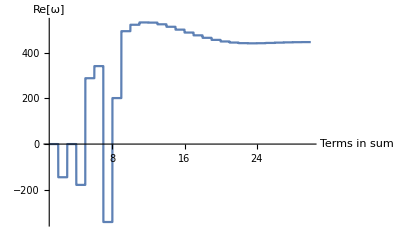

```mathematica
Plot[Re[ωsol[NN]], {NN, 1, 30}, PlotRange -> All, AxesLabel->{"Terms in sum", "Re[ω]"}]
```

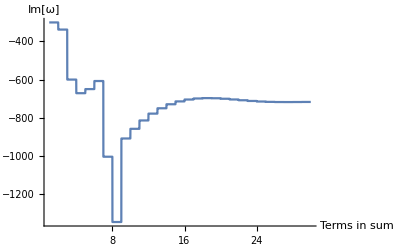

```mathematica
Plot[Im[ωsol[NN]], {NN, 1, 30}, PlotRange -> All, AxesLabel->{"Terms in sum", "Im[ω]"}]
```

From this plot, we can conclude that the result for ω converges for a finite number of terms in the sum. We can thus approximate ω as

```mathematica
ωval = ωsol[40]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

446.456-716.758 ⅈ

Let us now have a look at the quasinormal mode itself. As a reminder: 

	Φ(v, r) = 1/r ψ(r) e^(-ⅈ ω v)
	
with 

	ψ(x) = ∑_(n=0)^∞ (a_n(x - xh))^n

```mathematica
Psi[x_, Nit_]:=Sum[a[i]*(x-xh)^(i),{i,0,Nit}] /. ω -> ωval;
```

Has to be convergent for 0<x<xh (=0.01)

```mathematica
Plot3D[Re[Psi[x, NN]], {x, 0, xh},{NN, 1, 40 }, PlotRange->All, AxesLabel->{x, "Terms in sum", "Re[ψ]"}]
```

-Graphics3D-

```mathematica
Plot[Evaluate[Table[Re[Psi[x, NN]], {x, 0, 0.01, 0.005}]],{NN, 1, 40 }, PlotRange->All, AxesLabel->{x, "Terms in sum", "Re[ψ]"}]
```

General::ivar: 0.002 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of -(Sum`SumParserDump`res (Series[-0.018009,{0.001,1/100,0}]+(-1+j) j Series[0.000111,{0.001,1/100,0}]+j Series[2.9983×10^-6-(0.+2.×10^-6 ⅈ) ω,{0.001,1/100,0}]))/((-1+j) j Series[0.000111,{0.001,1/100,0}]+j Series[2.9983×10^-6-(0.+2.×10^-6 ⅈ) ω,{0.001,1/100,0}]).

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

$Aborted

```mathematica
QNM[v_, r_, NN_] := 1/r Psi[1/r,NN] Exp[-ⅈ ωval v]
```

```mathematica
Plot3D[Re[QNM[v, r, 10]], {v, 0, 0.05}, {r, rh, 1000}, AxesLabel-> {v, r, Φ}, PlotRange->{{0, 0.05}, {rh, 1000}, {-0.0003, 0.001}}, BoxRatios->{1, 1, 0.7}]
```

-Graphics3D-